```mathematica
Clear["Global`*"]
```

```mathematica
p1={0,1/Sqrt[3]};
p2={-1/2,-1/(2*Sqrt[3])};
p3={1/2,-1/(2*Sqrt[3])};
```

```mathematica
g1=RegionPlot[Sqrt[(x-p1[[1]])^2+(y-p1[[2]])^2]+Sqrt[(x-p2[[1]])^2+(y-p2[[2]])^2]+Sqrt[(x-p3[[1]])^2+(y-p3[[2]])^2]<3,{x,-1,1},{y,-1,1},BoundaryStyle-> Directive[Black,Thick],Frame->False];
g2=Graphics[{Gray,Circle[{0,0},1]}];
g3=Graphics[{Gray,Line[{p1,p2,p3,p1}],Black,PointSize[Large],Point[{p1,p2,p3}]}];
g4=Graphics[{Text[Style["A",FontFamily->"Times New Roman",Italic,22],p1+{0,0.1}],
Text[Style["B",FontFamily->"Times New Roman",Italic,22],p2+{-0.07,-0.07}],
Text[Style["C",FontFamily->"Times New Roman",Italic,22],p3+{0.07,-0.07}]}];
```

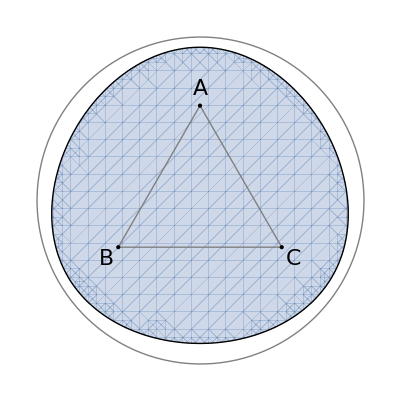

```mathematica
Show[g1,g2,g3,g4]
```

```mathematica
area=NIntegrate[Boole[Sqrt[(x-p1[[1]])^2+(y-p1[[2]])^2]+Sqrt[(x-p2[[1]])^2+(y-p2[[2]])^2]+Sqrt[(x-p3[[1]])^2+(y-p3[[2]])^2]<3],{x,-1,1},{y,-1,1},WorkingPrecision->20]
```

2.5716233808812113805